# Data Wrangling, Model Testing, and Model Analysis for Object-Oriented Models in the Wolfram Language

## Workshop # 232 40th International System Dynamics Conference Frankfurt, Germany & Online | July 22, 2022 Guido Wolf Reichert (BSL Management Suport) and Jan Brugård (Wolfram MathCore)

## Introduction

Wolfram Language?! Why should we bring models to programming environments?

### Let’s take 5 minutes to introduce Wolfram Mathematica \[MathematicaIcon] and the Wolfram Language\[WolframLanguageLogo]

#### Functional programming & symbolic computation

Mathematica (the main platform to run the Wolfram Language) is a Computer Algebra System (CAS).
Everything is essentially an expression, where the head can be thought of as a kind of label or type:

head[ e_1, e_2, ...]

Note, that square brackets [ ] in the Wolfram Language enclose a function’s (or more generally an expression’s) arguments. Braces { } collect elements in lists, while parentheses ( ) determine precedence of operations.

Looking at atomic expressions (we cannot further split these into subexpressions), we see that symbols are first class citizens:

```mathematica
Map[AtomQ] @ { 1, 1.2, "Hello", x } (* Map[func] @ { a, b, c} gives { func[a], func[b], func[c]} *)
```

{True,True,True,True}

```mathematica
Map[Head] @ { 1, 1.2, "Hello", x }
```

{Integer,Real,String,Symbol}

In the WL we can immediately do symbolic, mathematical computation, i.e., we do not need to assign numerical values.

```mathematica
x * x
```

If we look at the explict or full form, we see that indeed everything is an expression.

```mathematica
a + b c //FullForm
```

Take the antiderivative of a symbolic expression.

```mathematica
∫2 Sin[4x]ⅆx (* The internal FullForm of this is Integrate[ 2 Sin[4 x], x ]and we could have used it instead *)
```

-1/2 Cos[4 x]

And arrive back at the outset by taking the first derivative.

```mathematica
D[ % , x]  (* % can be used to refer to the last output; we could have written this as ∂_x -1/2Cos[4 x]*)
```

We could have used natural language input (press = at the beginning of a new line) to do this:

WolframAlphaQueryParseResults

Next to using precise symbolic computation we also have infinite precision for exact numbers:

```mathematica
Precision[π]
```

∞

```mathematica
N[π, 1000 ]
```

3.141592653589793238462643383279502884197169399375105820974944592307816406286208998628034825342117067982148086513282306647093844609550582231725359408128481117450284102701938521105559644622948954930381964428810975665933446128475648233786783165271201909145648566923460348610454326648213393607260249141273724587006606315588174881520920962829254091715364367892590360011330530548820466521384146951941511609433057270365759591953092186117381932611793105118548074462379962749567351885752724891227938183011949129833673362440656643086021394946395224737190702179860943702770539217176293176752384674818467669405132000568127145263560827785771342757789609173637178721468440901224953430146549585371050792279689258923542019956112129021960864034418159813629774771309960518707211349999998372978049951059731732816096318595024459455346908302642522308253344685035261931188171010003137838752886587533208381420617177669147303598253490428755468731159562863882353787593751957781857780532171226806613001927876611195909216420199

#### Plotting

We can plot expressions.

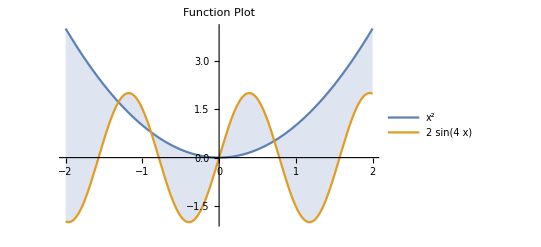

```mathematica
plot = Plot[ { x^2, 2Sin[4 x] }, {x,-2,2}, 
PlotLabel -> Style["Function Plot", "Subtitle", Gray], 
PlotLegends->"Expressions", 
Filling-> {1-> {2}}
]
```

... find the x values for graph intersections.

```mathematica
NSolveValues[ x^2 == 2 Sin[4 x], x, Reals]
```

{-1.31179,-0.886309,0.,0.719873}

And “map” a function over this list to generate a list of tuples (aka points).

```mathematica
points = % //Map[ Function[x, {x, x^2}]] (* in other words take a solution Subscript[x, sol] and return a tupel {x_(sol,) f[x_(sol])} *)
```

{{-1.31179,1.72078},{-0.886309,0.785544},{0.,0.},{0.719873,0.518218}}

These points can then be added as an “Epilog” to the plot. (A “Prolog” would be in the background, as it is drawn first.)

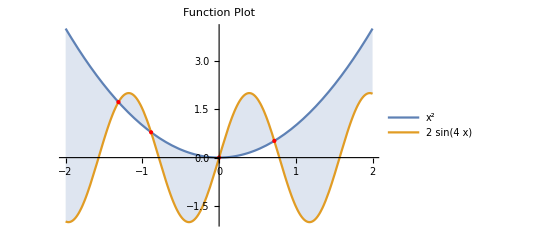

```mathematica
Plot[ { x^2, 2Sin[4 x] }, {x,-2,2}, 
PlotLabel -> Style["Function Plot", "Subtitle", Gray], 
PlotLegends->"Expressions", 
Filling-> {1-> {2}},
Epilog->{
Red,
PointSize[Medium],
Point @ points
}
]
```

#### Differential Equations

We can solve elementary symbolic differential equations, for example the following third order expontential delay system with a constant inflow:

```mathematica
DSolve[
{
x1'[t] == inflow - x1[t]/(delayTime/3),
x2'[t] == x1[t]/(delayTime/3)-x2[t]/(delayTime/3),
x3'[t] == x2[t]/(delayTime/3)-x3[t]/(delayTime/3),
x1[0]==initialX1,
x2[0]== initialX2,
x3[0]== initialX3
}
,
{ x1, x2, x3}
,
t
]//First /* TableForm
```

x1→Function[{t},1/3 ⅇ^(-(3 t)/delayTime) (-delayTime inflow+delayTime ⅇ^((3 t)/delayTime) inflow+3 initialX1)]
x2→Function[{t},(ⅇ^(-(3 t)/delayTime) (-delayTime^2 inflow+delayTime^2 ⅇ^((3 t)/delayTime) inflow+3 delayTime initialX2-3 delayTime inflow t+9 initialX1 t))/(3 delayTime)]
x3→Function[{t},(ⅇ^(-(3 t)/delayTime) (-2 delayTime^3 inflow+2 delayTime^3 ⅇ^((3 t)/delayTime) inflow+6 delayTime^2 initialX3-6 delayTime^2 inflow t+18 delayTime initialX2 t-9 delayTime inflow t^2+27 initialX1 t^2))/(6 delayTime^2)]

#### Knowledge Representation & Access

A tremendous amount of data stored for Entities can be immediately accessed and processed.

WolframAlphaQueryParseResults

9.63142×10^6 km^2

WolframAlphaQueryParseResults

Fri 14 Mar 1879

Often we are interested in a subset of entities, i.e., we apply a filter or a query.

```mathematica
EntityClass["Country","EuropeanUnion"]
```

European Union

... and look at the entities

```mathematica
EntityClass["Country","EuropeanUnion"]//EntityList
```

{Austria,Belgium,Bulgaria,Croatia,Cyprus,Czech Republic,Denmark,Estonia,Finland,France,Germany,Greece,Hungary,Ireland,Italy,Latvia,Lithuania,Luxembourg,Malta,Netherlands,Poland,Portugal,Romania,Slovakia,Slovenia,Spain,Sweden}

What are the properties that we may be interested in for the entity “country”?

```mathematica
EntityProperties["Country"]//Short//rasterize
```

-Graphics-

So let’s get the population in 2000 for the countries in the EU and make this a nice looking table using the UN country code to identify countries.

```mathematica
EntityClass["Country","EuropeanUnion"]//RightComposition[
EntityList,
Map @ Function[ country,
<|EntityProperty["Country", "UNCode"]@country ->EntityProperty["Country", "Population", { "Date"-> 2000 }]@country |> 
],
Dataset
]
```

We can also visualize geographic data.

```mathematica
EntityClass["City",{EntityProperty["City","Country"]->Entity["Country","France"],EntityProperty["City","Population"]->GreaterThan[100000]}]//EntityList//Map[Function[entity, Tooltip[ entity, EntityProperty["City", "Name"]@ entity, TooltipStyle -> Large ]]]//GeoListPlot
```

-Graphics-

#### Further Information

An Elementary Introduction to the Wolfram Language

Wolfram Language: Fast Introduction for Programmers

Wolfram Language: Fast Introduction for Math Students

Wolfram Language & System Documentation Center

### Building modern data science techniques into modeling software versus importing models into mature data science environments

Houghton and Siegel (2015) in introducing PySD come to the conclusion: 
It makes much more sense to import models to powerful data science environments than to wait until methods are eventually integrated in the system dynamics software.

So how is system dynamics and systems modeling in general integrated into the Wolfram Language?

Systems Modeling is found in the section “Engineering Data & Computation”:

The guide on “System Model Analytics & Design” gets us right into this workshops further topics.

## Model Creation and Import

How can we create system models in the WL and how can we access models that we or others have already built?

### Object–oriented modeling using pre-built components in Wolfram SystemModeler (a quick recap of Workshop #231)

#### Using classes from the Business Simulation Library (BSL)

The classes for building system dynamics models came from the Business Simulation Library (BSL), which is a modern implementation of system dynamics in Modelica making use of acausal “physical” connectors (think: pipe fittings).

#### Hello World! example using component-based modeling

In Workshop #231 we introduced component-based modeling in Wolfram System Modeler—starting out with a simple Hello World! example.

#### Building larger models in a hierarchical fashion

We then showed how larger models can be build in a distributed, object-oriented fashion that is especially amenable to working in a team, to using version control systems like Git, and to documenting models in an integrated fashion (documentation needs to be integrated into the modeling environment ...).

### Creating models programmatically in the Wolfram Language

We will not address creating models programmatically in the WL in this workshop, but instead provide a few pointers.

#### Connect pre-built components from within a program

You can use ConnectSystemModelComponents to use pre-built components from a library and connect them to build a SystemModel.

#### Build a model using a different modeling paradigm

Using CreateSystemModel you can turn a systems model, i.e., a model following a different modeling paradigm, into a SystemModel that can be used and connected as a Modelica model. Systems models can be one of the following:

StateSpaceModel

TransferFunctionModel

AffineStateSpaceModel

NonlinearStateSpaceModel

DiscreteInputOutputModel

Using this you can integrate (partial) models from other domains into your Modelica models—after all, whatever your background, we are interested indynamical systems.

#### Create a data model by sampling from a function

By sampling from a function to come up with an interpolated curve, CreateDataSystemModel let’s you build an information source for other models to use.

### Importing existing models

#### Import a textual model written in Modelica

In Workshop #231 we started out with a textual Modelica model for a teacup cooling to room temperature.
Let’s import it as a string (note that strings inside are” escaped” using \ .

```mathematica
$teaCupFromString = ImportString[
"model TeaCupTextual \"Textual model for cooling cup\"
  import BusinessSimulation.Units.{Time,Rate};
  extends BusinessSimulation.Icons.Example;
  // parameters
  parameter Real initTempCup(unit = \"degC\") = 90 \"Initial temperature in the cup\";
  parameter Real tempRoom(unit = \"degC\") = 20 \"Temperature in the room\";
  parameter Time adjTime(displayUnit = \"min\") = 600 \"Time constant for adjustment process\";
  // stock & flow variables
  Real tempCup(start = initTempCup, unit = \"degC\") \"Temperature in the cup is modeled as a stock\";
  Rate heatFlow(displayUnit = \"1/min\") \"Outflow of heat from the cup\";
equation
  heatFlow = (tempRoom - tempCup) / adjTime;
  der(tempCup) = heatFlow;
end TeaCupTextual;"
,
"MO" (* type MO for Modelica models *)
]
```

-Graphics-

Looking at the Modelica code after the input shows that it is interpreted correctly as a model written in the Modelica language.

```mathematica
$teaCupFromString["ModelicaDisplay"]
```

model TeaCupTextual "Textual model for cooling cup"
  import BusinessSimulation.Units.{Time,Rate};
  extends BusinessSimulation.Icons.Example;
  // parameters
  parameter Real initTempCup(unit = "degC") = 90 "Initial temperature in the cup";
  parameter Real tempRoom(unit = "degC") = 20 "Temperature in the room";
  parameter Time adjTime(displayUnit = "min") = 600 "Time constant for adjustment process";
  // stock & flow variables
  Real tempCup(start = initTempCup, unit = "degC") "Temperature in the cup is modeled as a stock";
  Rate heatFlow(displayUnit = "1/min") "Outflow of heat from the cup";
equation
  heatFlow = (tempRoom - tempCup) / adjTime;
  der(tempCup) = heatFlow;
end TeaCupTextual;

#### Importing SystemModeler Models (.mo), Archives (.sma) or directly accessing installed models

Smaller models can be loaded as .mo file.

Import[ "filename.mo", "MO"]

In case we do not have SystemModeler installed, we need to import a library or larger model (package.mo) and its data. This is best done using Import or CloudImport and the .sma format that packs models as an archive.

Import[ "filename", "SMA”] or CloudImport[ “uri” ]

If the model has dependencies and is not distributed as a “total model” then we have to make sure that all the libraries needed are imported as well.

If we have loaded a library or a modeling project in a local installation of SystemModel, we can immediately access it.

```mathematica
$teaCupComponentBasedModel1 = SystemModel["ISDC2022_Workshops.Examples.TeaCupComponentBased1"]
```

-Graphics-

## Model Exploration

How do models tell us before we even simulate them?

### SystemModel properties

Once we have loaded (or created) a SystemModel, we can explore its properties.

```mathematica
Dataset[ SystemModel[ "ISDC2022_Workshops.Examples.TeaCupTextual", "Properties"],DatasetTheme->"Detailed"]//rasterize
```

-Graphics-

#### Summary

Typically at first we will want to look at a model summary.

```mathematica
SystemModel[ "ISDC2022_Workshops.Examples.TeaCupComponentBased1", "Summary"]//rasterize
```

-Graphics-

#### Icon View

We can access the icon for any class.

```mathematica
SystemModel[ "TeaCupComponentBased1", { "ModelicaIcon", ImageSize -> 200, Frame-> None}]
```

-Graphics-

#### Diagram View

... inspect a model’s diagram.

```mathematica
SystemModel[ "ISDC2022_Workshops.Examples.TeaCupComponentBased2", "Diagram"]
```

-Graphics-

#### Text View

As discussed for entering models above, we can access the Modelica code either as a pure string.

```mathematica
SystemModel["ISDC2022_Workshops.Examples.TeaCupTextual", "ModelicaString" ]
```

model TeaCupTextual "Textual model for cooling cup"
  import BusinessSimulation.Units.{Time,Rate};
  extends BusinessSimulation.Icons.Example;
  // parameters
  parameter Real initTempCup(unit = "degC") = 90 "Initial temperature in the cup";
  parameter Real tempRoom(unit = "degC") = 20 "Temperature in the room";
  parameter Time adjTime(displayUnit = "min") = 600 "Time constant for adjustment process";
  // stock & flow variables
  Real tempCup(start = initTempCup, unit = "degC") "Temperature in the cup is modeled as a stock";
  Rate heatFlow(displayUnit = "1/min") "Outflow of heat from the cup";
equation
  heatFlow = (tempRoom - tempCup) / adjTime;
  der(tempCup) = heatFlow;
  annotation(Documentation(info = "<html>
<p class=\"aside\">This information is part of the ISDC2022 Workshops package.</p>
<p>
This is a stylized model of heat loss for a cup of tea. The model given here is textual only, e.g., there are no components with connections.
</p>
<p>
The temperature in the cup is modeled as a stock (<code>tempCup</code>) with a flow (<code>heatFlow</code>). The outflow of heat, i.e., a negative flow of heat, can be obtained as <code>(tempRoom - tempCup)/adjTime</code>.
</p>
</html>", figures = {Figure(title = "Temperature", identifier = "temp", preferred = true, plots = {Plot(curves = {Curve(y = tempCup)}, __Wolfram_markerAppearances = {MarkerAppearance(marker = "d3d94"), MarkerAppearance(marker = "e4da3")})}, caption = "Tea cup cooling down to room temperature", __Wolfram_markers = {Marker(identifier = "e4da3", position = MarkerPosition(x = 300, xUnit = "s")), Marker(identifier = "d3d94", position = MarkerPosition(x = 600, xUnit = "s"))}, __Wolfram_intervals = {Interval(identifier = "556e0", startMarker = "e4da3", endMarker = "d3d94")})}), experiment(StopTime = 3600, __Wolfram_DisplayTimeUnit = "min"), Diagram(coordinateSystem(extent = {{-148.5, -105}, {148.5, 105}}, preserveAspectRatio = true, initialScale = 0.1, grid = {5, 5}), graphics = {Text(visible = true, origin = {3.28, 10}, rotation = 33.802, textColor = {76, 112, 136}, extent = {{-86.72, -12}, {86.72, 12}}, textString = "textual model only", fontName = "Lato Black")}));
end TeaCupTextual;

... or in a color-coded version. Note, that the annotations—used to store experiment settings, documentation, plots etc.—are nicely hidden behind a » .

```mathematica
SystemModel["ISDC2022_Workshops.Examples.TeaCupTextual", "ModelicaDisplay" ]
```

model TeaCupTextual "Textual model for cooling cup"
  import BusinessSimulation.Units.{Time,Rate};
  extends BusinessSimulation.Icons.Example;
  // parameters
  parameter Real initTempCup(unit = "degC") = 90 "Initial temperature in the cup";
  parameter Real tempRoom(unit = "degC") = 20 "Temperature in the room";
  parameter Time adjTime(displayUnit = "min") = 600 "Time constant for adjustment process";
  // stock & flow variables
  Real tempCup(start = initTempCup, unit = "degC") "Temperature in the cup is modeled as a stock";
  Rate heatFlow(displayUnit = "1/min") "Outflow of heat from the cup";
equation
  heatFlow = (tempRoom - tempCup) / adjTime;
  der(tempCup) = heatFlow;
 »;
end TeaCupTextual;

### A closer look at model structure, equations, and parameters

The information contained in a model diagram can be used for exploration as well.

```mathematica
SystemModel[ "ISDC2022_Workshops.Examples.TeaCupComponentBased1", "Diagram" ]
```

-Graphics-

#### Components used

Which components are used in the model?

```mathematica
bslSystemModelComponentDatabase[ SystemModel["ISDC2022_Workshops.Examples.TeaCupComponentBased1"] ]//Dataset//rasterize
```

-Graphics-

#### Model connections

Connections are shown between connectors (e.g., adjTime.y) as a list of undirected edges <-> .

```mathematica
SystemModel[ "ISDC2022_Workshops.Examples.TeaCupComponentBased1", "Connections" ]
```

{adjTime.y<->heatLoss.u2,heatLoss.y<->losingHeat.u,losingHeat.portB<->cloud.massPort,tempCup.outflow<->losingHeat.portA,tempCup.y2<->tempDifference.u1,tempDifference.y<->heatLoss.u1,tempRoom.y<->tempDifference.u2}

Using the “database” of components above, we can transform this into a graph with directed edges (causal connections)  to detect feedback loops.

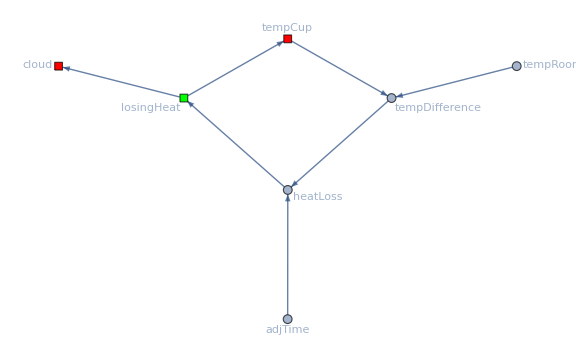

```mathematica
bslSystemModelGraph[ SystemModel[ "ISDC2022_Workshops.Examples.TeaCupComponentBased1" ], ImageSize -> Large, GraphLayout-> "SpringElectricalEmbedding" ]
```

#### Model equations

Finally, we can inspect the equations in the model (using Method → {“Elimination”-> All} ) to get rid of a lot of the (necessary)  object-oriented overhead. (At the moment, we are also neglecting discrete-event related functionality and strip equations of WhenEvent expressions.

```mathematica
SystemModel[ "ISDC2022_Workshops.Examples.TeaCupComponentBased1","SystemEquations",Method-> {"Elimination"-> All} ]//DeleteCases[WhenEvent[ ___]]//TableForm
```

-losingHeat.B_rate IndependentPhysicalQuantity[Rate][t]==(tempDifference.y IndependentPhysicalQuantity[][t])/(adjTime.value Time)
tempDifference.y IndependentPhysicalQuantity[][t]==-tempRoom.value IndependentPhysicalQuantity[]+tempCup.x IndependentPhysicalQuantity[][t]
losingHeat.y IndependentPhysicalQuantity[Rate][t]==If[losingHeat.useA_rate IndependentPhysicalQuantity[][t]&&losingHeat.useB_rate IndependentPhysicalQuantity[][t],-losingHeat.B_rate IndependentPhysicalQuantity[Rate][t],0]
tempCup.x IndependentPhysicalQuantity[]'[t]==-losingHeat.y IndependentPhysicalQuantity[Rate][t]

#### Parameters and their values

... and find out about the (top level) parameters for a model and their values.

```mathematica
SystemModel[ "ISDC2022_Workshops.Examples.TeaCupTextual","TopParameterNames" ]
```

{initTempCup IndependentPhysicalQuantity[],tempRoom IndependentPhysicalQuantity[],adjTime Time}

```mathematica
SystemModel[ "ISDC2022_Workshops.Examples.TeaCupTextual","ParameterValues" ]
```

{initTempCup IndependentPhysicalQuantity[]→90,tempRoom IndependentPhysicalQuantity[]→20,adjTime Time→600}

#### Exogenous inputs

Even though we all try to have our models be endogenous ;-) there will be models and components that have external information inputs.

```mathematica
SystemModel["ISDC2022_Workshops.Examples.PeopleExpress.RunWithExogenousInputs", "InputVariables" ]
```

{u_peoplesFare IndependentPhysicalQuantity[],u_travelFrequency IndependentPhysicalQuantity[]}

## Analyzing Model Behavior

### Making use of pre-configured plots and experiment settings

In the examples, that we build in the previous workshop, we stored plots and indicated that some of these plots are the default plot. We also set up an experiment for the model, so this information can be used immediately.

```mathematica
SystemModel["ISDC2022_Workshops.Examples.TeaCupTextual", "PlotNames"]
```

{Temperature}

```mathematica
SystemModel["ISDC2022_Workshops.Examples.TeaCupTextual", "SimulationSettings"]//Map @ ReplaceAll[ time_?NumericQ :> UnitConvert[ Quantity[time, "Seconds"], "Minutes"]]
```

<|DisplayTimeUnit→Minutes,StopTime→60 min|>

```mathematica
SystemModel[ "ISDC2022_Workshops.Examples.PeopleExpress.TestFleet_1", "SimulationSettings"]
```

<|DisplayTimeUnit→Years,StartTime→62472816000,StopTime→62693568000|>

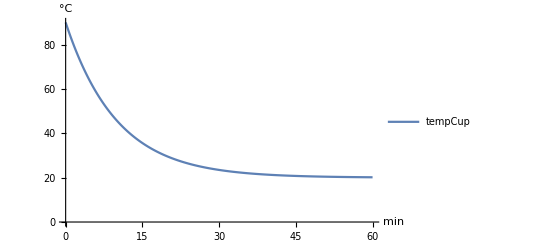
-Graphics-Temperature. Tea cup cooling down to room temperature

```mathematica
SystemModelPlot[ "ISDC2022_Workshops.Examples.TeaCupTextual"]
```

We can use the stored plot, but modify the simulation settings. We can use Quantity or use Ctrl =  to conveniently work with whatever unit of time we prefer (all our models will run in “Seconds”).
The result will be a SystemModelSimulationData object.

```mathematica
$sim = SystemModelSimulate[ SystemModel["ISDC2022_Workshops.Examples.TeaCupTextual"], { 0,Quantity[30, "Minutes"] } ] (* we could have entered: Quantity[ 30, "Minutes" ]*)
```

SystemModelSimulationData[…]

```mathematica
SystemModelSimulationData[…]
```

Same plot—different simulation times.

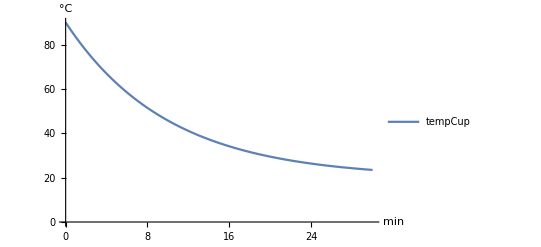
-Graphics-Temperature. Tea cup cooling down to room temperature

```mathematica
SystemModelPlot[ $sim ]
```

### Automated model tests

In the Resources/Notebooks directory you will find PeopleExpressModelTests.nb and we can run the tests within that testing notebook right here.

```mathematica
$testNotebook = FileNameJoin[ { NotebookDirectory[], "PeopleExpressModelTests.nb" } ]
```

D:\git-local\isdc-2022-workshops\ISDC2022_Workshops\Resources\Notebooks\PeopleExpressModelTests.nb

```mathematica
$report = TestReport @ $testNotebook
```

TestReportObject[…]

In case of failures, we can look at the failed tests more closely using the following code.

```mathematica
Column/@(Normal/@$report["TestsFailed"])//TabView
```

123

## Deploying Models

### Overview

FMI 		: 	Functional Mockup Interface
FMU 		: 	Functional Mockup Unit
MCTT	:	Modelica CombiTimeTable
UDS		:	Universal Deployment System

### Dashbords in the Cloud

## Helper Functions

#### rasterize

Datasets certainly look nice, but interactivity slows down the front-end; making output a static picture in a sufficient resolution isoften  a good compromise.

```mathematica
rasterize = OperatorApplied[Rasterize][ImageResolution-> 300];
```

#### bslSystemModelComponentDatabase

Come up with an Association (aka “dictionary” in other languages) of a model’s components that can later be used for looking up vars and building bridges back to conventional system dynamics diagramming.

```mathematica
ClearAll[bslSystemModelComponentDatabase];
bslSystemModelComponentDatabase[ model_SystemModel ]:=model["Components"]//RightComposition[
OperatorApplied[Cases][ Element[ name_String, SystemModel[ component_String, True]]:> Association["Name"-> name, "Class" -> component]]
];
```

#### bslSystemModelGraph

Want to look at a causal loop diagram instead?

```mathematica
ClearAll[ bslSystemModelGraph ];
bslSystemModelGraph::usage = "bslSystemModelGraph[model] will return a graph with causal connections shown as directed edges.";
bslSystemModelGraph[ model_SystemModel, opts : OptionsPattern[] ] := bslSystemModelGraph[ model["Connections"], bslSystemModelComponentDatabase[ model ], opts ];
bslSystemModelGraph[ connections_ , componentDatabase_ , opts : OptionsPattern[] ]:=
With[
{
inputPattern =  ___~~".u"~~___~~EndOfString,
outputPattern = ___ ~~ ".y" ~~ ___ ~~ EndOfString,
stockQ = Function[ key, componentDatabase//RightComposition[
Query[ SelectFirst[ #Name ==key&], "Class" ],
OperatorApplied[Not@*StringFreeQ]["Stocks"| "Cloud"]
] 
],
flowQ = Function[ key, componentDatabase//RightComposition[
Query[ SelectFirst[ #Name ==key&], "Class" ],
OperatorApplied[Not@*StringFreeQ]["Flows"|"SourcesOrSinks" ]
] 
],
toVertices=Function[ edges, edges//RightComposition[
ReplaceAll[ DirectedEdge[ a_, b_]| UndirectedEdge[a_, b_ ] :>Sequence[a,b]],
Union
]
]
}
,
(* replace input <-> output and output <-> input with directed edges *)
connections//RightComposition[
ReplaceAll[ c1_String <-> c2_String :> c2->c1 /; And[
StringMatchQ[c1, inputPattern ],
StringMatchQ[c2, outputPattern ]
]
],
ReplaceAll[ c1_String <-> c2_String :> c1 -> c2 /; And[
StringMatchQ[c1, outputPattern ],
StringMatchQ[c2, inputPattern ]
]
],
(* get rid of connector names at the end of component names *)
ReplaceAll[x_String :>StringDelete[x,"." ~~___]],
(* make flow <-> stock connections directed edges *)
ReplaceAll[ f_String <-> s_String | s_String <->f_String :> f-> s /; And[
stockQ @ s,
flowQ @ f
]
],
(* draw a graph *)
Function[ edges,
With[
{ 
stockList = Select[ toVertices @ edges,stockQ ],
flowList = Select[ toVertices @ edges, flowQ ]
}
, 
Graph[ edges,
Sequence @@ FilterRules[ Flatten @ { opts }, Options[Graph]],
VertexLabels-> "Name",
VertexShapeFunction-> Union[ Thread[ stockList -> "Square" ], Thread[ flowList -> "Square" ]],
VertexStyle-> Union[ Thread[ stockList -> Red ], Thread[ flowList -> Green ] ]
]
]
]
]
]
```